{0.08,0.09,0.12,0.08,0.1,0.1,0.11}

FittedModel[0.50267 x+2.26126]

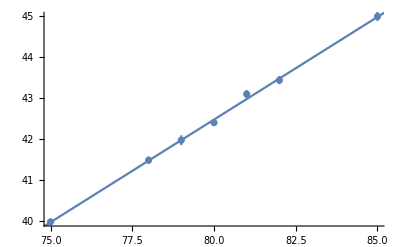

{81.1243,2.02542}

{91.9267,2.17077}

{90.6535,2.14304}

```mathematica
Needs["ErrorBarPlots`"]
fits = {{39.97,0.08,75},{41.48,0.09,78},{41.97,0.12,79},{42.40,0.08,80}, {43.10,0.1,81},{43.44,0.1,82},{45.00,0.11,85}};
fits2 = Map[{{#[[3]], #[[1]]}, ErrorBar[#[[2]]]}&, fits];
Whalfmax = {43.04, 0.09};
errors = Map[#[[2]]&,fits]
nlm = NonlinearModelFit[Map[{#[[1,1]],#[[1,2]]} &, fits2],A*x+B, {A,B},x, Weights->100/errors^2]
Show[ErrorListPlot[fits2], Plot[nlm[x],{x,74.5,85.5}]]
Bfit=B/.nlm["BestFitParameters"];
Afit = A/.nlm["BestFitParameters"];
Aerr = nlm["ParameterErrors"][[1]];
Berr = nlm["ParameterErrors"][[2]];
(*Systematic error from QCD factor: +- 0.05*)
Mass[x_, xerr_] := {x/Afit - Bfit/Afit, Sqrt[xerr^2/Afit^2 + x^2/Afit^4 *Aerr^2 + Berr^2/Afit^2 + Bfit^2/Afit^4 * Aerr^2]}
Mass[Whalfmax[[1]], Whalfmax[[2]]]
(*Z mass without cuts*)
Mass[48.47, 0.12]
(*Z mass with transverse momentum <20*)
Mass[47.83, 0.05]
```

```mathematica
(*scale factor is 0.3*)
fits = {{40.03,0.09,75},{41.49,0.09, 78},{41.97,0.12,79},{42.41,0.09,80},{43.10,0.1,81},{43.45,0.09,82},{45.00,0.11,85}};
fits2 = Map[{{#[[3]], #[[1]]}, ErrorBar[#[[2]]]}&, fits];
Whalfmax = {42.96, 0.07};
errors = Map[#[[2]]&,fits];
nlm = NonlinearModelFit[Map[{#[[1,1]],#[[1,2]]} &, fits2],A*x+B, {A,B},x, Weights->100/errors^2];
Show[ErrorListPlot[fits2], Plot[nlm[x],{x,74.5,85.5}]];
Bfit=B/.nlm["BestFitParameters"];
Afit = A/.nlm["BestFitParameters"];
Aerr = nlm["ParameterErrors"][[1]];
Berr = nlm["ParameterErrors"][[2]];
(*Systematic error from QCD factor: +- 0.05*)
Mass[x_, xerr_] := {x/Afit - Bfit/Afit, Sqrt[xerr^2/Afit^2 + x^2/Afit^4 *Aerr^2 + Berr^2/Afit^2 + Bfit^2/Afit^4 * Aerr^2]}
(*W mass*)
Mass[Whalfmax[[1]], Whalfmax[[2]]]
```

{80.9452,2.06872}

{92.0286,2.22354}

{90.7412,2.19531}

```mathematica
(*scale factor is 0.4*)
fits = {{39.96,0.08,75},{41.47,0.09,78},{41.96,0.12,79},{42.39,0.08,80},{43.09,0.1,81},{43.44,0.1,82},{44.99,0.11,85}};
fits2 = Map[{{#[[3]], #[[1]]}, ErrorBar[#[[2]]]}&, fits];
Whalfmax = {42.96, 0.07};
errors = Map[#[[2]]&,fits];
nlm = NonlinearModelFit[Map[{#[[1,1]],#[[1,2]]} &, fits2],A*x+B, {A,B},x, Weights->100/errors^2];
Show[ErrorListPlot[fits2], Plot[nlm[x],{x,74.5,85.5}]];
Bfit=B/.nlm["BestFitParameters"];
Afit = A/.nlm["BestFitParameters"];
Aerr = nlm["ParameterErrors"][[1]];
Berr = nlm["ParameterErrors"][[2]];
(*Systematic error from QCD factor: +- 0.05*)
Mass[x_, xerr_] := {x/Afit - Bfit/Afit, Sqrt[xerr^2/Afit^2 + x^2/Afit^4 *Aerr^2 + Berr^2/Afit^2 + Bfit^2/Afit^4 * Aerr^2]}
(*W mass*)
Mass[Whalfmax[[1]], Whalfmax[[2]]]
```

{80.9815,1.98951}

{91.9351,2.13786}

{90.6628,2.11024}